# Terrario

## Premise

Grid of RGB cells

Red, green, and blue are all distinct species

Opacity determined by energy

Cells have energy, color, position, brain

Brain contains instructions on basic behavior

A cell can kill an adjacent cell of another color by expending more energy than that cell has

Includes empty cells which have a constant base energy

Living cells passively gain energy

Cells can transfer energy to neighbors

Cell behavior is controlled by DNA

Sequence of rules determining which action to take based on information from surrounding cells

## Plan

Construct cell and grid data structures

Construct modification functions for nearby cells

Set rules for cell creation, destruction, and energy usage

Construct instruction set for dna

Dynamically modify dna during reproduction

## Mockup

```mathematica
newCell[]:=<|"color"->RandomColor[RGBColor[_,_,_,1]],"energy"->1,"dna"->Nothing|>
newGrid[size_]:=Table[newCell[],size,size]
getColors[cells_]:=Map[#color& ,cells,{2}]
getBlends[colors_]:=ArrayFilter[Blend[Blend/@#]&,colors,{1,1}]
```

```mathematica
grid=newGrid[5];
```

```mathematica
ListAnimate[ArrayPlot/@NestList[getBlends,getColors[grid],5]]
```

## Rules

One or zero cells in each space of the grid

Cells start with 1 energy and produce 1 energy per tick spent alive

Cells can only interact with directly adjacent cells

Cells die on reaching 0 energy

## Possible Actions

Reproduce in adjacent cell by spending 3 energy

Can control mutations

Transfer energy between adjacent cells

Can reduce alien energy by spending same amount

## Implementation

Grid is an array of associations, each representing a cell with all its info

Cells contain an RGBColor[_,_,_,_], numerical energy, and a list of rules for dna

Dead cells are represented as white cells with no energy

## Prototype

```mathematica
Clear[newCell]
```

```mathematica
newCell[]:=<|"color"->RandomColor[RGBColor[_,_,_,1]],"energy"->1,"dna"->Nothing|>
newCell[color_]:=<|"color"->color,"energy"->1,"dna"->Nothing|>
deadCell[]:=<|"color"->RGBColor[1,1,1,1],"energy"->0,"dna"->Nothing|>
newGrid[size_]:=Table[newCell[],size,size]
sparseGrid[size_,chance_]:=Table[If[RandomReal[]<chance,newCell[],deadCell[]],size,size]
getColors[cells_]:=Map[#color& ,cells,{2}]
cullCells[cells_]:=Map[If[#energy<1,deadCell[],#]&,cells,{2}]
```

```mathematica
cells=sparseGrid[10,.1];
ArrayPlot[getColors[cells]]
```

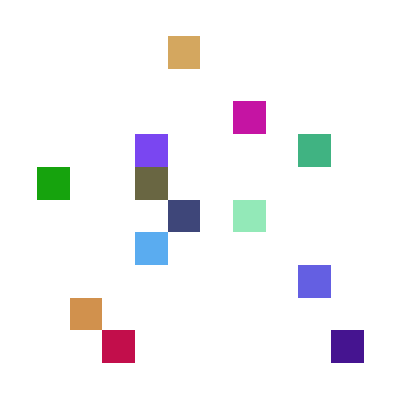

```mathematica
dna =IntegerDigits[ RandomInteger[{0,255}],2]
```

{1,0,1,1,1,1,0,1}